# Vaje iz Mathematice, 3. del

### 1. naloga:

Nariši graf funkcije y=a sin (k x+n), pri čemer boš lahko vrednosti parametrov a, k in n spreminjal v obsegu od -3 do 3. Območje risanja omeji na [-5,5]×[-5,5]. Enoti na x in y osi naj bosta enako veliki.

```mathematica
Manipulate[Plot[a* Sin[k x + n],{x,-5,5},PlotRange->{-5,5},AspectRatio -> Automatic],{a,-3,3},{k,-3,3},{n,-3,3}]
```

### 2. naloga:

Nariši graf premice y=k x+n  in na isti sliki še pravokotnico nanjo, ki gre skozi točko T(x_0,y_0), pri čemer boš lahko spreminjal vrednosti parametrov k, n, x_0 in y_0. Na sliki označi z majhnim krogcem, kje leži točka T.

```mathematica
Manipulate[Plot[{k x+n,(x0 -x)/k+y0},{x,-5,5},PlotRange->{-5,5}, AspectRatio->Automatic,Epilog->Point[{x0,y0}]],{k,-3,3},{n,-3,3},{x0,-3,3},{y0,-3,3}]
```

### 3. naloga:

Definiraj funkcijo  f(x)=(x(x-2))^2/(x^2+1) ter nariši njen graf skupaj s tangento v točki x_0, tako da boš lahko spreminjal vrednost parametra x_0. Na sliki označi z majhnim krogcem, kje se tangenta dotika grafa funkcije.

```mathematica
f[x_]:= (x(x-2)^2)/(x^2+1)
```

```mathematica
odvod = D[f[x],x]
```

-(2 (-2+x)^2 x^2)/((1+x^2)^2)+(-2+x)^2/(1+x^2)+(2 (-2+x) x)/(1+x^2)

```mathematica
Manipulate[Plot[{f[x],(D[f[t],t] /. {t-> x0})*(x-x0)+f[x0]},{x,-10,10},PlotRange->{-10,10},AspectRatio->Automatic,Epilog->Point[{x0,f[x0]}]],{x0,-5,5}]
```

### 4. naloga:

Definiraj funkcijo  g(x)=-x^3+8  in nariši njen graf nad intervalom [-3,3].

Izračunaj ničlo funkcije g.

Izračunaj ploščino lika, ki ga (v prvem kvadrantu) omejujeta koordinatni osi in graf te funkcije.

Še enkrat nariši graf funkcije g nad istim intervalom, le da bo tokrat območje, katerega ploščino si izračunal, pobarvano.

```mathematica
g[x_] := -x^3 +8
```

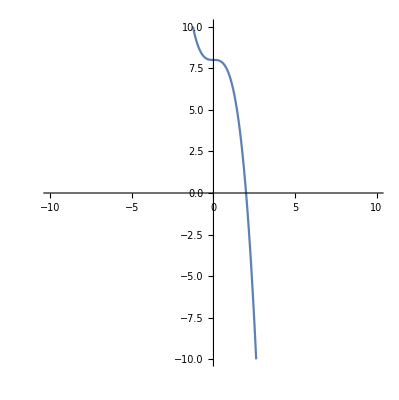

```mathematica
Plot[g[x],{x,-10,10},PlotRange->{-10,10},AspectRatio->Automatic]
```

```mathematica
nicla = x /. First[Solve[g[x]== 0,x,Reals]]
```

2

```mathematica
Integrate[g[x],{x,0,nicla}]
```

12

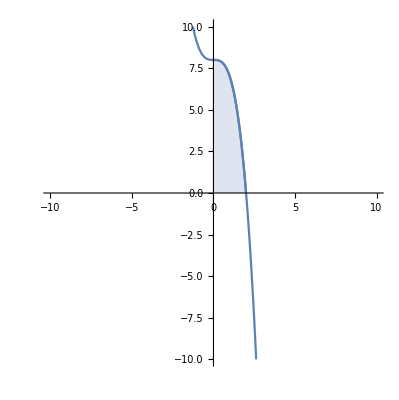

```mathematica
Show[Plot[g[x],{x,-10,10},PlotRange->{-10,10},AspectRatio->Automatic],Plot[g[x],{x,0,nicla},Filling->Axis]]
```

### 5. naloga:

Definiraj funkciji  h(x)=x^2-8  in  k(x)=-x^2+10  ter nariši njuna grafa.

Poišči njuni presečišči.

Izračunaj ploščino lika, ki ga omejujeta grafa teh dveh funkcij.

Še enkrat nariši grafa obeh funkcij, le da bo tokrat območje, katerega ploščino si izračunal, pobarvano.

```mathematica
h[x_]:=x^2-8
k[x_]:=-x^2+10
```

```mathematica
nicli=x/.Solve[h[x]== k[x],x]
```

{-3,3}

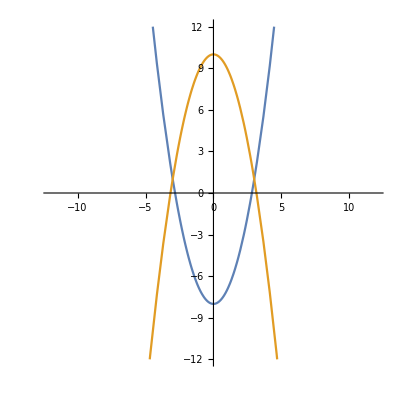

```mathematica
Plot[{h[x],k[x]},{x,-12,12},PlotRange->{-12,12},AspectRatio->Automatic]
```

```mathematica
Integrate[k[x]-h[x],{x,nicli[[1]],nicli[[2]]}]
```

72

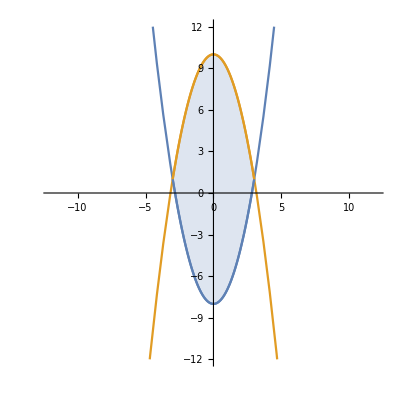

```mathematica
Show[Plot[{h[x],k[x]},{x,-12,12},PlotRange->{-12,12},AspectRatio->Automatic],Plot[{h[x],k[x]},{x,nicli[[1]],nicli[[2]]},PlotRange->{-12,12},AspectRatio->Automatic,Filling->{1-> {2}}]]
```

### 6. naloga:

Nariši graf funkcije u(x)=x^3-8 x^2+100  na intervalu [-5,10] in pobarvaj površino med grafom in vodoravno osjo na intervalu [a,b], kjer lahko parametra a in b spreminjaš od -5 do 10. Začetna vrednost parametra a naj bo 1, začetna vrednost parametra b pa 8. Nariši še navpični črti med vodoravno osjo in grafom v točkah x=a  in  x=b. Črti naj bosta enake barve kot graf funkcije.

```mathematica
u[x_]:= x^3-8x^2+100
```

```mathematica
Manipulate[Show[Plot[u[x],{x,-5,10},Epilog->Line[{{{a,0},{a,u[a]}},{{b,0},{b,u[b]}}}]],Plot[u[x],{x,a,b},PlotRange->{-200,500},AspectRatio->1/1.2,Filling->Axis]],{{a,1},-5,10},{{b,8},-5,10}]
```

### 7. naloga:

Nariši graf, ki prikazuje, kako se funkcije  f_n(x)=(1+x/n)^n  približujejo svoji limiti  g(x)=ⅇ^x. Graf naj prikazuje funkcije f_1,f_2, ...,f_10 (vse enake barve) in funkcijo g (drugačne barve). Sam izberi primeren interval.

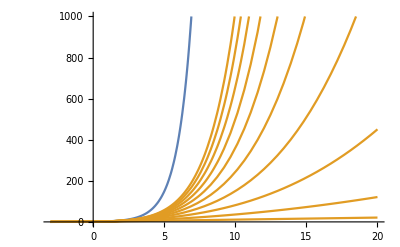

```mathematica
Plot[{E^x,Table[(1+x/n)^n,{n,1,10}]},{x,-3,20},PlotRange->{0,1000}]
```

### 8. naloga:

Definiraj funkcijo, ki sprejme naravno število in vrne število njegovih različnih prafaktorjev.

Poišči vsa tista števila med 1 in 1000, ki imajo največje število različnih prafaktorjev. Namig: oglej si funkcijo MaximalBy.

```mathematica
SteviloPrafaktorjev[n_]:= Length[FactorInteger[n]]
```

```mathematica
SteviloPrafaktorjev[770]
```

4

```mathematica
MaximalBy[Range[1,1000],SteviloPrafaktorjev]
```

{210,330,390,420,462,510,546,570,630,660,690,714,770,780,798,840,858,870,910,924,930,966,990}

### 9. naloga:

Tabeliraj numerične vrednosti funkcije  sin (2x)√x v točkah 0, π/12,π/6,π/4,π/3,(5π)/12,π/2.

Katera od dobljenih vrednosti je najbližja številu 1/3? Namig: uporabiš lahko funkcijo MinimalBy.

```mathematica
vrednosti=N[Map[Sin[2*#]*Sqrt[#]&,{0,Pi/12,(5*Pi)/12,Pi/6,Pi/4,Pi/3,Pi/2}]]
```

{0.,0.255832,0.572057,0.626657,0.886227,0.886227,0.}

```mathematica
MinimalBy[vrednosti,Abs[#-1/3]&]
```

{0.255832}

### 10. naloga:

Definiraj funkcijo  f(x)=sin (3x)+x^2-5  in nariši njen graf na intervalu [-3,3].

Z numeričnim reševanjem enačb (FindRoot) poišči ničli funkcije f

Izračunaj ploščino med grafom funkcije in vodoravno osjo na intervalu med ničlama.

Še enkrat nariši graf funkcije in pri tem pobarvaj območje, katerega ploščino si izračunal.

```mathematica
f[x_]:= Sin[3x]+x^2-5
```

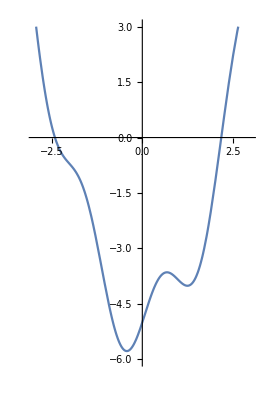

```mathematica
Plot[f[x],{x,-3,3},PlotRange -> {-6,3},AspectRatio->Automatic]
```

```mathematica
nicli=x/.{FindRoot[f[x],{x,-2}],FindRoot[f[x],{x,2}]}
```

{-2.41113,2.17912}

```mathematica
Abs[Integrate[f[x],{x,nicli[[1]],nicli[[2]]}]]
```

14.9584

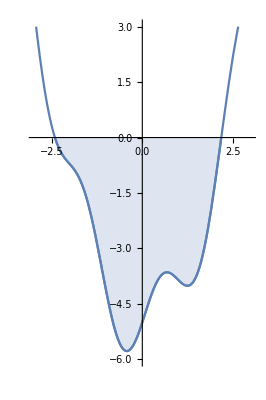

```mathematica
Show[Plot[f[x],{x,-3,3},PlotRange -> {-6,3},AspectRatio->Automatic],Plot[f[x],{x,nicli[[1]],nicli[[2]]},Filling->Axis]]
```

### 11. naloga:

Praštevilski dvojček sta taki praštevili p in q, da velja q=p+2. Na primer, števili 71 in 73 tvorita praštevilški dvojček. Katera izmed prvih 100 praštevil nastopajo v praštevilskem dvojčku? Sestavi seznam, ki jih vsebuje.

Sestavi seznam praštevilskih dvojčkov, pri čemer je manjše število v dvojčku eno od prvih 100 praštevil.

```mathematica
Select[Prime[Range[100]],PrimeQ[#-2]||PrimeQ[#+2]&]
```

{3,5,7,11,13,17,19,29,31,41,43,59,61,71,73,101,103,107,109,137,139,149,151,179,181,191,193,197,199,227,229,239,241,269,271,281,283,311,313,347,349,419,421,431,433,461,463,521,523}

### 12. naloga:

Izračunaj  (3001
576).

Razcepi dobljeno vrednost.

Izmed vseh prafaktorjev izberi tiste, ki se v razcepu števila pojavijo več kot enkrat.

S pomočjo faktorizacije dokaži, da je  ∑_(k=0)^10 (10
k)x^k=(x+1)^10

### 13. naloga:

Nariši graf implicitno podane funkcije  y^2-y-2=(x^2-1)^3  na območju [-5,5]×[-5,5].

Poišči ekplicitno obliko funkcije  y=f(x)  pri pogoju y≥0. Se pravi, definiraj funkcijo f, da bo veljalo f(x)≥0 in (f(x))^2-f(x)-2=(x^2-1)^3 za vse x.

Preveri, ali res velja  (f(x))^2-f(x)-2=(x^2-1)^3

Nariši graf funkcije f na [-2,2]×[0,5]. Enoti na oseh naj bosta enaki.

### 14. naloga:

Nariši graf implicitno podane funkcije  |x|^(2/3)+|y|^(2/3)=1  na območju [-1,1]×[-1,1]

Prikaži, kako se spreminja graf implicitne krivulje  |x|^p+|y|^p=1  za vrednosti parametra p∈[0,4]  z začetno vrednostjo 2.

Pri kateri vrednosti p leži točka (1/3,1/3) na grafu krivulje?

### 15. naloga:

Naj bo p(x)=a x^2+b x+c. Za nekatere vrednosti koeficientov a, b, c se zaporedje p(1), p(2), p(3),... začne s praštevili. Na primer, če je p(x)=x^2+3x+1, dobimo zaporedje, katerega prvih pet členov so praštevila. Poiščimo take vrednosti 1≤a, b, c≤25, da bodo p(1),p(2),p(3),...,p(15) praštevila. Do rešitve pridemo v naslednjih korakih:

Definiraj funkcijo, ki sprejme seznam koeficientov a,b,c in vrne True, če so vrednosti polinoma a x^2+b x+c praštevila za vsa naravna števila 1≤x≤15. Namig: kaj naredi Apply[And,seznam]?

Sestavi seznam vseh možnih trojic števil {a,b,c}, kjer velja 1≤a,b,c≤25.

Iz seznama vseh trojic izberi tiste, ki določajo zaporedje, ki ima na začetku vsaj 15 praštevil.